# Ions in an AC Electric Field: Strong Long-Range Repulsion between Oppositely Charged Surfaces

## Data S1

Paweł Jan Żuk

## First order in V_0 properties

The solution proportional to V_0 is presented

### Loading the library

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<firstOrder`
```

### Evaluation of formula and plotting

### Introducing the numerical values of parameters

δVal stands for value of δ,
 κVal stands for value of κ,
  χVal stands for value of χ,
   ωVal stands for value of ω,
    zpVal stands for z_+

```mathematica
δVal=0.1;
κVal=1;
χVal=2;
ωVal=10^-1;
zpVal=1;
```

### Evaluating the numerical values of eigenvalues (eq. 33) and eigenvectors (eq. 34)

In this part κ and z_+ can be an arbitrary number not only 1 as in the supplementary information.

```mathematica
λ[1]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[1]][[1]]]];
λ[2]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[1]][[2]]]];
λ[3]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[1]][[3]]]];
λ[4]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[1]][[4]]]];
v[1]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[2]][[1]]]];
v[2]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[2]][[2]]]];
v[3]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[2]][[3]]]];
v[4]=With[{ω=ωVal,ϵ=δVal,κ=κVal,χ=χVal,zp=zpVal},Evaluate[matrixEigensystem[1][[2]][[4]]]];
```

### Evaluation of numerical coefficients for plotting

```mathematica
t1={c1[1],c1[2],c1[3],c1[4],c1[5],c1[6]};
t2=N[({c1[1],c1[2],c1[3],c1[4],c1[5],c1[6]}/.analConst[1][1][[1]]/.v11->v[1][[1]]/.v31->v[3][[1]]/.λ1->λ[1]/.λ3->λ[3]/.v33->v[3][[3]]/.v13->v[1][[3]]/.v12->v[1][[2]]/.v32->v[3][[2]]/.ϵ->δVal/.κ->κVal/.zp->zpVal),100];
numSol[1]=MapThread[Rule,{t1,t2},1];
```

### Time dependent solution to the first order equations

We plot the functions 
V_0(Exp[ⅈ t] (n^(1))_(+,1)+Exp[-ⅈ t] (n^(1))_(+,-1))=V_02 Re Exp[ⅈ t] (n^(1))_(+,1),
V_0(Exp[ⅈ t] (n^(1))_(-,1)+Exp[-ⅈ t] (n^(1))_(-,-1))=V_02 Re Exp[ⅈ t] (n^(1))_(+,1),
V_0(Exp[ⅈ t](ϕ^(1))_1+Exp[-ⅈ t](ϕ^(1))_-1)=V_0 2 Re Exp[ⅈ t](ϕ^(1))_1

```mathematica
valV0=1.;
Manipulate[Plot[{
2Re[valV0((analf[1][x]Exp[I tm]/.numSol[1]))/.v11->v[1][[1]]/.v31->v[3][[1]]/.λ1->λ[1]/.λ3->λ[3]/.v33->v[3][[3]]/.v13->v[1][[3]]/.v12->v[1][[2]]/.v32->v[3][[2]]/.ϵ->δVal/.κ->κVal/.zp->zpVal],
2Re[valV0((analp[1][x]Exp[I tm]/.numSol[1]))/.v11->v[1][[1]]/.v31->v[3][[1]]/.λ1->λ[1]/.λ3->λ[3]/.v33->v[3][[3]]/.v13->v[1][[3]]/.v12->v[1][[2]]/.v32->v[3][[2]]/.ϵ->δVal/.κ->κVal/.zp->zpVal],
2Re[valV0((analm[1][x]Exp[I tm]/.numSol[1]))/.v11->v[1][[1]]/.v31->v[3][[1]]/.λ1->λ[1]/.λ3->λ[3]/.v33->v[3][[3]]/.v13->v[1][[3]]/.v12->v[1][[2]]/.v32->v[3][[2]]/.ϵ->δVal/.κ->κVal/.zp->zpVal]},
{x,0,1.},
PlotRange->All,PlotLegends->{"ϕ","p","m"},PlotStyle->{Black,Red,Blue}],{tm,0,2π}]
```

### Analytical Formula

To view the result in this section please delete the semicolons at the end of the lines.

(n^(1))_(+,1) ions distribution function

```mathematica
analp[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

d/dx(n^(1))_(+,1) ions distribution function

```mathematica
analdp[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

(n^(1))_(-,1) ions distribution function

```mathematica
analm[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

d/dx(n^(1))_(-,1) ions distribution function

```mathematica
analdm[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

(ϕ^(1))_1 potential function

```mathematica
analf[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

d/dx(ϕ^(1))_1 ions distribution function

```mathematica
analdf[1][x]/.First[analConst[1][1]]/.v11->vs[1][[1]]/.v12->vs[1][[2]]/.v13->vs[1][[3]]/.v31->vs[3][[1]]/.v32->vs[3][[2]]/.v33->vs[3][[3]]/.λ1->λs[1]/.λ3->λs[3];
```

## Second order in V_0 properties

The solution proportional to V_0^2 is presented
From now on there is an assumption that z_+=1 and z_-=1 which means that κ=1

### Loading the library

```mathematica
<<secondOrder`
```

### Evaluation and plotting

### Introducing the numerical values of parameters

The parameters for the function evaluation can be given similar as in the first order case by directly providing them to functions.
They can also be introduced as calculated from the physical values (all given in their SI units):
ϵiVal stands for dielectric constant ϵ,
kbVal stands for the Boltzmann’s constant k_B,
TVal stands for the temperature of the solution T,
eVal stands for the unit charge e,
zpVal stands for z_+,
zmVal stands for z_-,
nMM stands for milimolar concentration that is N_A/m^3 with Avogadro’s nuber N_A=6.022 10^23

```mathematica
ϵiVal=80 8.854 10^-12;
kbVal=1.38 10^-23;
TVal=300;
eVal=1.602 10^-19;
zpVal=1;
zmVal=1;
nMM=6.022 10^23;
```

There are also parameters that will treated as variables so we will define them further
LVal stands for the system size L,
DpVal stands for the diffusion coefficient of the positive ion D_+,
DmVal stands for the diffusion coefficient of the negative ion D_-,
ωfVal stands for the external forcing frequency ω_f,
n0 stands for the bulk electrolyte concentration n_0,

```mathematica
LVal;
DpVal;
DmVal;
ωfVal;
n0Val;
```

The set of calculated dimensioned values
dimλ stands for the dimensioned Debye’s length λ,
dimL stands for the dimensioned system size L,
dimωRc stands for the dimensioned RC frequency ω_RC=τ_RC^-1,
dimωλ stands for the dimensioned Debye’s frequency ω_λ=τ_λ^-1,
dim L stands for the dimensioned system size frequency ω_L=τ_L^-1

```mathematica
dimλ=Sqrt[(ϵiVal kbVal TVal)/(eVal^2 n0 zpVal)];
dimL=LVal;
dimωRC=(DpVal/(dimλ dimL));
dimωλ=(DpVal/dimλ^2);
dimωL=(DpVal/dimL^2);
```

Next the dimensionless quantities can be calculated
dTodLχ stands for diffusion coefficients ratio χ=D_-/D_+,
dTodLκ stands for the ratio of ionic charges κ=z_+/z_-,
dTodLδ stands for the ratio of the Debye’s length to the system size δ=λ/L,
dTodLω stands for the dimensionless forcing frequency with respect to the Debye’s frequency ω=ω_f/ω_λ

```mathematica
dTodLχ=DmVal/DpVal;
dTodLκ=zpVal/zmVal;
dTodLϵ=dimλ/dimL;
dTodLω=ωfVal/dimωλ;
dTodLω=ωfVal/dimωλ;
```

Simple example of usage of these notation is presented below as a code necessary to create the Figure S4 showing what are the frequencies of the forcing (10^5 Hz) in comparison to the frequencies connected to ionic diffusion coefficients and system size.

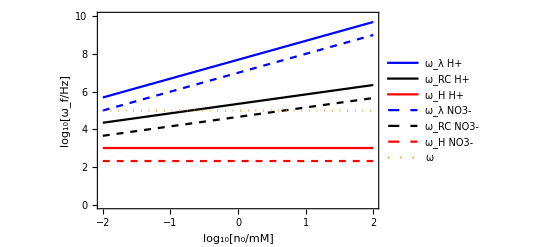

```mathematica
plotSampleOmega=Plot[{
Log10[dimωλ]/.DpVal->9.3 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
Log10[dimωRC]/.DpVal->9.3 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
Log10[dimωL]/.DpVal->9.3 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
Log10[dimωλ]/.DpVal->1.9 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
Log10[dimωRC]/.DpVal->1.9 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
Log10[dimωL]/.DpVal->1.9 10^-9/.LVal->3 10^-6/.n0->nMM 10^x,
5},
{x,-2,2},
PlotRange->{0,10},Frame->True,Axes->False,
FrameLabel->{"log_10[n_0/mM]","log_10[ω_f/Hz]"},
PlotStyle->{{Plain,Blue},{Plain,Black},{Plain,Red},{Dashed,Blue},{Dashed,Black},{Dashed,Red},{Dotted,Orange}},
PlotLegends->{"ω_λ H+","ω_RC H+","ω_H H+","ω_λ NO3-","ω_RC NO3-","ω_H NO3-","ω"},
BaseStyle->Medium]
```

### Plotting the functions proportional to V_0^2

The functions presented here are complex thus in order to plot its value we first create the table and then a plot out of it.

#### The excess ionic density n(x) (eq. 46)

funCaln[x,χ,δ,ω,κ]
that takes arguments in dimensionless form. 
The below example was used to generate the panel A in Figure S5.

```mathematica
accur=100;
χTable={0.5,1,2,5};
δVal=10^-2;
ωVal=10^-2;
plotSizeInX=5 δVal;
dataPlot1=Table[{
x/δVal,
Chop[funCaln[
  SetAccuracy[x,accur],
  SetAccuracy[#,accur],
  SetAccuracy[δVal,accur],
  SetAccuracy[ωVal,accur],
  SetAccuracy[κVal,accur]]]},
{x,0,plotSizeInX,plotSizeInX/100}]&/@χTable;
```

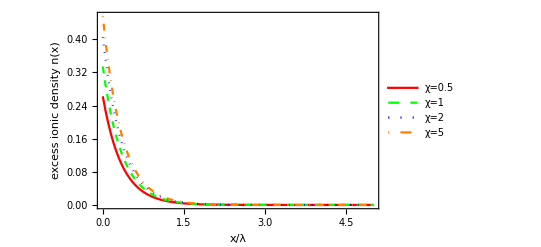

```mathematica
obrazekGestosc=ListPlot[dataPlot1,
PlotRange->All,Joined->True,
PlotLegends->Placed[{
  "χ="<>TextString[χTable[[1]]],
  "χ="<>TextString[χTable[[2]]],
  "χ="<>TextString[χTable[[3]]],
  "χ="<>TextString[χTable[[4]]]},
Below],
Frame->True,Axes->False,BaseStyle->Medium,
PlotStyle->{{Plain,Red},{Dashed,Green},{Dotted,Blue},{DotDashed,Orange}},
FrameLabel->{{"excess ionic density n(x)",None},
{"x/λ","δ="<>TextString[δVal]<>",ω="<>TextString[ωVal]}},PlotRange->All]
```

#### The excess ionic density at the wall n(0)

funCaln[0,χ,δ,ω,κ]
that takes arguments in dimensionless form. 
The below example was used to generate the panel B in Figure S5.

```mathematica
accur=100;
δVal=10^-2;
ωTable={10^-2,10^-1,1,10};
dataPlot2=Table[{
s,
Log10[Chop[funCaln[
  SetAccuracy[0,accur],
  SetAccuracy[s,accur],
  SetAccuracy[δVal,accur],
  SetAccuracy[#,accur],
  SetAccuracy[κVal,accur]]]]},
{s,0.1,4.,0.1}]&/@ωTable;
```

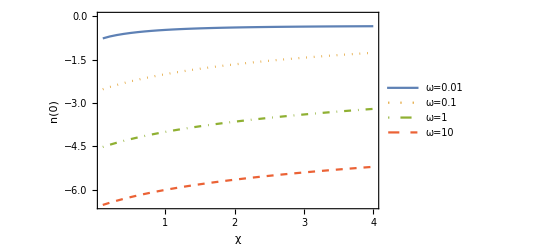

```mathematica
obrazekGestosc=ListPlot[dataPlot2,
PlotRange->All,Joined->True,
PlotLegends->Placed[{
  "ω="<>TextString[ωTable[[1]]],
  "ω="<>TextString[ωTable[[2]]],
  "ω="<>TextString[ωTable[[3]]],
  "ω="<>TextString[ωTable[[4]]]},
Below],
Frame->True,Axes->False,BaseStyle->Medium,
PlotStyle->{{Plain,Red},{Dashed,Green},{Dotted,Blue},{DotDashed,Orange}},
FrameLabel->{{"n(0)",None},
{"χ","δ="<>TextString[δVal]}},PlotRange->All]
```

#### The excess negative charge density ρ(x) (eq. 45)

funCalrho[x,χ,δ,ω,κ]
that takes arguments in dimensionless form. 
The below example was used to generate the panel A in Figure S6.

```mathematica
accur=100;
χTable={0.5,1,2,5};
δVal=10^-2;
ωVal=10^-2;
plotSizeInX=5 δVal;
dataPlot3=Table[{
x/δVal,
Chop[funCalrho[
  SetAccuracy[x,accur],
  SetAccuracy[#,accur],
  SetAccuracy[δVal,accur],
  SetAccuracy[ωVal,accur],
  SetAccuracy[κVal,accur]]]},
{x,0,plotSizeInX,plotSizeInX/100}]&/@χTable;
```

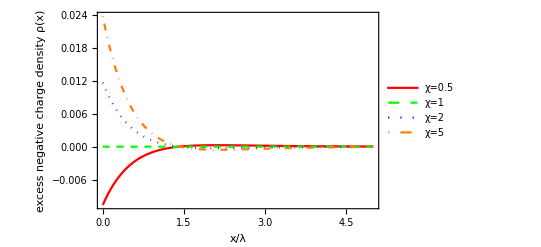

```mathematica
obrazekGestosc=ListPlot[dataPlot3,
PlotRange->All,Joined->True,
PlotLegends->Placed[{
  "χ="<>TextString[χTable[[1]]],
  "χ="<>TextString[χTable[[2]]],
  "χ="<>TextString[χTable[[3]]],
  "χ="<>TextString[χTable[[4]]]},
Below],
Frame->True,Axes->False,BaseStyle->Medium,
PlotStyle->{{Plain,Red},{Dashed,Green},{Dotted,Blue},{DotDashed,Orange}},
FrameLabel->{{"excess negative charge density ρ(x)",None},
{"x/λ","δ="<>TextString[δVal]<>",ω="<>TextString[ωVal]}},PlotRange->All]
```

#### Total excess negative ionic charge Q

funCalQ[χ,δ,ω,κ]
that takes arguments in dimensionless form. 
The below example was used to generate the panel B in Figure S6.

```mathematica
accur=2000;
δVal=10^-2;
ωTable={10^-2,10^-1,1,10};
dataPlot4=Table[{
s,
Chop[funCalQ[
  SetAccuracy[s,accur],
  SetAccuracy[δVal,accur],
  SetAccuracy[#,accur],
  SetAccuracy[κVal,accur]]]},
{s,0.1,4.,0.1}]&/@ωTable;
```

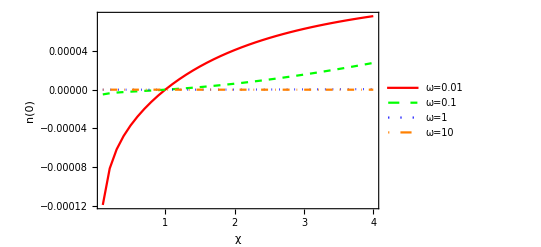

```mathematica
obrazekGestosc=ListPlot[dataPlot4,
PlotRange->All,Joined->True,
PlotLegends->Placed[{
  "ω="<>TextString[ωTable[[1]]],
  "ω="<>TextString[ωTable[[2]]],
  "ω="<>TextString[ωTable[[3]]],
  "ω="<>TextString[ωTable[[4]]]},
Below],
Frame->True,Axes->False,BaseStyle->Medium,
PlotStyle->{{Plain,Red},{Dashed,Green},{Dotted,Blue},{DotDashed,Orange}},
FrameLabel->{{"n(0)",None},
{"χ","δ="<>TextString[δVal]}},PlotRange->All]
```

### Analytical expressions for the functions proportional to V_0^2

To view expression please delete the semicolon at the end of the line.

the analytical expressions for functions n(x)

```mathematica
funCaln[x,χ,δ,ω,κ];
```

the analytical expressions for functions ρ(x)

```mathematica
funCalrho[x,χ,δ,ω,κ];
```

the analytical expressions for functions Q

```mathematica
funCalQ[x,χ,δ,ω,κ];
```